```mathematica
Quit[]
```

## Set Notebook Directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Krzysztof\Desktop\Magisterka\Praca-magisterska\Maxim-axion

## Read data: q.csv

```mathematica
(*Step 1:Import the CSV file*)
data=Import["q.csv","CSV"];
(*Step 2: set the list*)
qList = data[[1]];

(*output the qList*)
(*qList*)
```

## Read data: Distributions.csv

```mathematica
(*Step 1:Import the CSV file*)
data=Import["Distributions.csv","CSV"];
(*******************************************************************************************)
(*Skip the header row and extract the first element from each subsequent row: there will be fa value*)
faList=data[[2;;,1]];

(*Output the list of first elements without the header*)
faList
faList[[119]]
(*******************************************************************************************)
(*Separate header and data*)
header=data[[1]];                 (*Extract the header row*)
dataWithoutHeader=data[[2;;]];   (*Extract the data without the header row*)

(*Skip the first element in each data row*)
distributionsQPow2=Rest/@dataWithoutHeader;
(*Output the processed data without header, `f(q) * q^2*)
(*distributionsQPow2[[1]]*)
(*Here we have to divide each elelemt by q^2, `f(q)`*)
distributions = Map[MapThread[Times,{#,qList^-2}]&,distributionsQPow2];
(* f(q) * q^3*)
distributionsQPow3 = Map[MapThread[Times,{#,qList}]&,distributionsQPow2];
(*distributions[[1]]*)
```

{10000000,15000000,20000000,25000000,30000000,35000000,40000000,45000000,50000000,55000000,60000000,65000000,70000000,75000000,80000000,85000000,90000000,95000000,100000000,105000000,110000000,115000000,120000000,125000000,130000000,135000000,140000000,145000000,150000000,155000000,160000000,165000000,170000000,175000000,180000000,185000000,190000000,195000000,200000000,205000000,210000000,215000000,220000000,225000000,230000000,235000000,240000000,245000000,250000000,255000000,260000000,265000000,270000000,275000000,280000000,285000000,290000000,295000000,300000000,305000000,310000000,315000000,320000000,325000000,330000000,335000000,340000000,345000000,350000000,355000000,360000000,365000000,370000000,375000000,380000000,385000000,390000000,395000000,400000000,405000000,410000000,415000000,420000000,425000000,430000000,435000000,440000000,445000000,450000000,455000000,460000000,465000000,470000000,475000000,480000000,485000000,490000000,495000000,500000000,505000000,510000000,515000000,520000000,525000000,530000000,535000000,540000000,545000000,550000000,555000000,560000000,565000000,570000000,575000000,580000000,585000000,590000000,595000000,600000000,605000000,610000000,615000000,620000000,625000000,630000000,635000000,640000000,645000000,650000000,655000000,660000000,665000000,670000000,675000000,680000000,685000000,690000000,695000000,700000000,705000000,710000000,715000000,720000000,725000000,730000000,735000000,740000000,745000000,750000000,755000000,760000000,765000000,770000000,775000000,780000000,785000000,790000000,795000000,800000000,805000000,810000000,815000000,820000000,825000000,830000000,835000000,840000000,845000000,850000000,855000000,860000000,865000000,870000000,875000000,880000000,885000000,890000000,895000000,900000000,905000000,910000000,915000000,920000000,925000000,930000000,935000000,940000000,945000000,950000000,955000000,960000000,965000000,970000000,975000000,980000000,985000000,990000000,995000000,1000000000}

600000000

## Draw row distribution

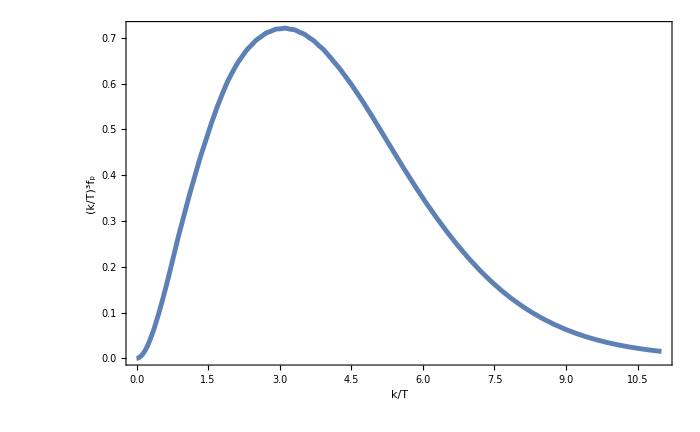

```mathematica
(*Helpfull function to create Transposed data, remeber that `i` will refer to vale of `f_a` in `faList`.*)
transposeData[i_,list_,listOfLists_List]:=Transpose[{list,listOfLists[[i]]}]
(*Create the plot*)
AxDistFunctionTab=transposeData[1,qList,distributionsQPow3]; (* f(q)*q^3 *)
AxDistFunction=Interpolation[AxDistFunctionTab,Method->"Spline",InterpolationOrder->3];
Plot[{AxDistFunction[x]},{x,0,11},Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},{Thickness[0.005],Orange,ColorData[97,2]}},ImageSize-> 700]
```

## Axion distribution function : find their fit

FittedModel[ⅇ^(63887.5-1.17645 (54305.5+√(1+x^2))) x^2 √(1+x^2)]

best fit parameters: {A→1.17645,b→-54305.5,μ→-63887.5}[]

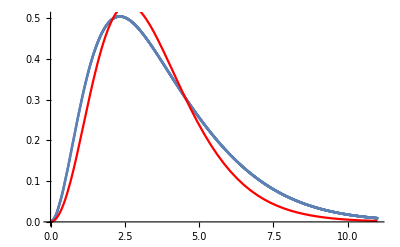

```mathematica
(*Set distrubution*)
AxDistFunctionTab=transposeData[10,qList,distributionsQPow3]; (* f(q)*q^3 *)
AxDistFunction=Interpolation[AxDistFunctionTab,Method->"Spline",InterpolationOrder->3];
(*Defined the approx axion distribution function*)
(*fApprox[x_,A_,b_,μ_]:=x^3*A(1/(Exp[x/b + μ]-1))*)
fApprox[x_,A_,b_,μ_]:=x^2 √(1+x^2)*(Exp[A(√(1+x^2)-b)+μ])^-1

(*Generate some sample data points*)
xmin = 0.0;
xmax = 11;
step = 0.005;
data=Table[{x,AxDistFunction[x]},{x,xmin,xmax,step}];
(*Initial guesses for parameters*)
initialGuesses={72.69732279066642, 0.9386200048727305,5.129280037899677 };

(*Perform the nonlinear fit*)
fit=NonlinearModelFit[data,fApprox[x,A,b,μ],{A,b,μ},x]
(*Extract best-fit parameters*)
bestFitParams=fit["BestFitParameters"];
Print["best fit parameters:"bestFitParams[]];

(*Visualize the fit*)
Show[ListPlot[data],Plot[fit[x],{x,xmin,xmax},PlotStyle->Red]]
```

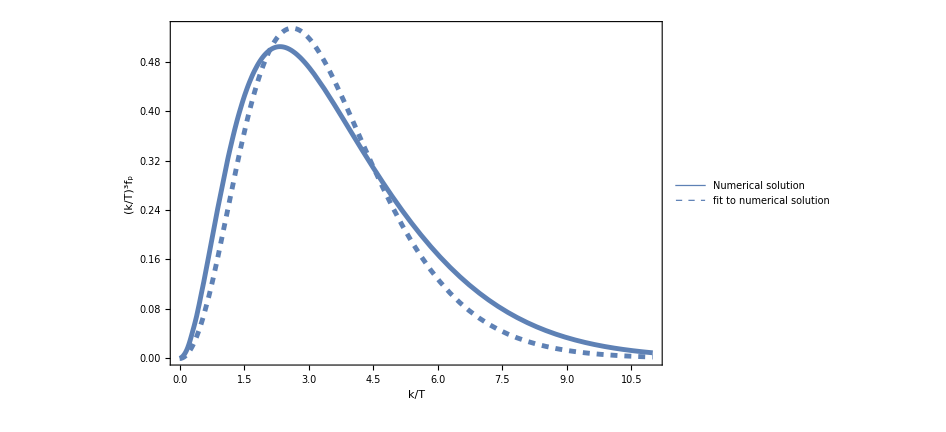

Distribution_and_fit_F9.png

```mathematica
plot = Show[Plot[{AxDistFunction[x], fit[x]},{x,0,11},Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},{Thickness[0.005],Orange,ColorData[97,2]}},

PlotLegends->{"Numerical solution","fit to numerical solution"},
ImageSize-> 700]]
(*save plot*)
Export["Distribution_and_fit_F9.png",plot]
(*show plot*)
(*plot*)
```